### Stochastic environmental changes u = 10^-1,m=10^-1 u = 10^-1,m=10^-5 u = 10^-5,m=10^-1

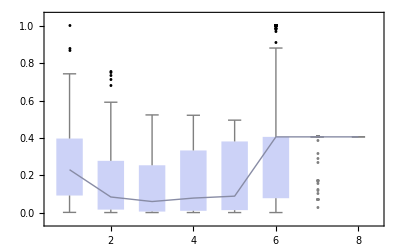
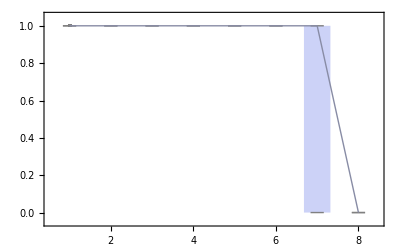
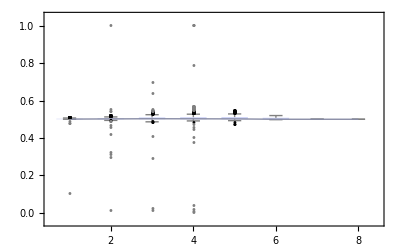

### Stochastic environmental changes T=100, T=200 , T=250

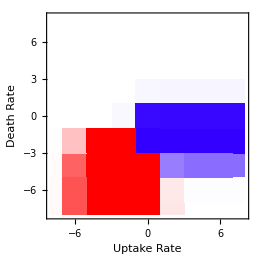
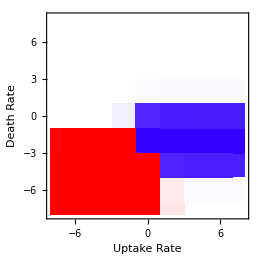
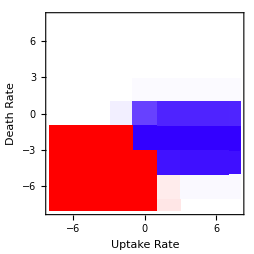

### Problem of fluctuation

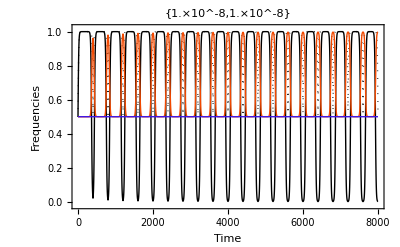
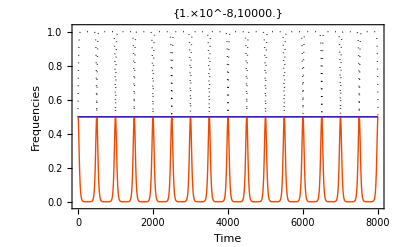

### Stochastic environmental changes T=100, T=200 , T=250, T=400

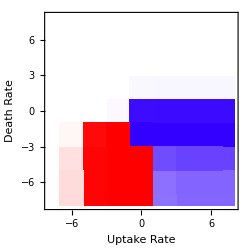
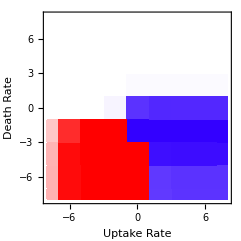
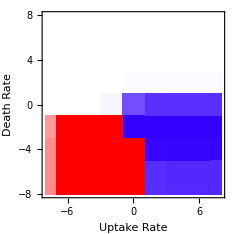
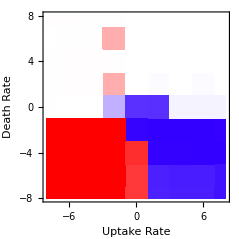

### Weird dynamics

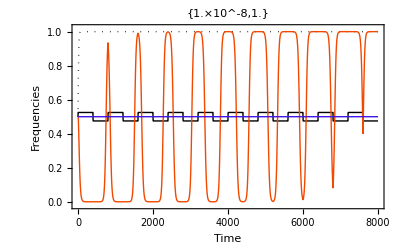

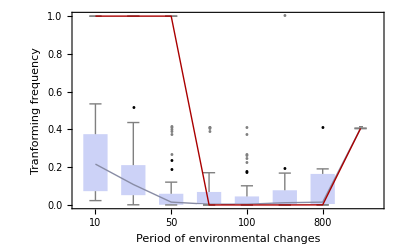
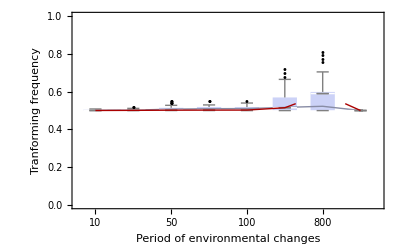
```mathematica
a1=-Graphics-;a2=-Graphics-;
```

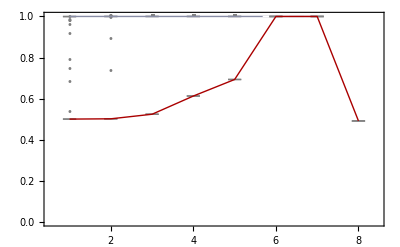
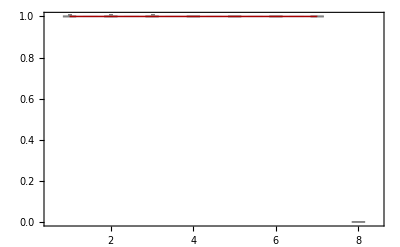
```mathematica
a4=-Graphics-;a3=-Graphics-;
```

```mathematica
GraphicsGrid[{{a1,a2},{a3,a4}},AspectRatio-> 0.65]
```

```mathematica
r1=Import["/Users/danesh/Documents/workspace/transformation/Res10.txt"];
r2=Import["/Users/danesh/Documents/workspace/transformation/Res50.txt"];
r3=Import["/Users/danesh/Documents/workspace/transformation/Res100.txt"];
r4=Import["/Users/danesh/Documents/workspace/transformation/Res320.txt"];
```

```mathematica
r1[[1]]
```

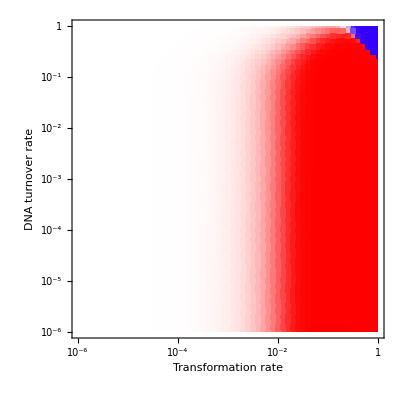

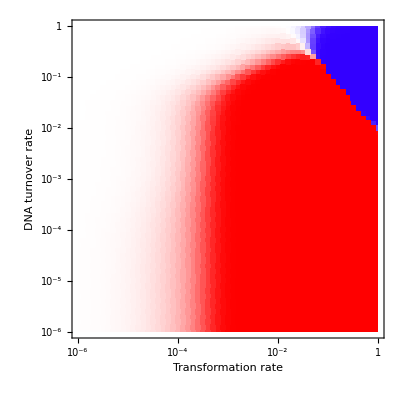

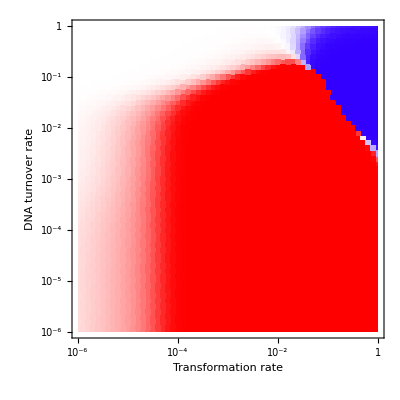

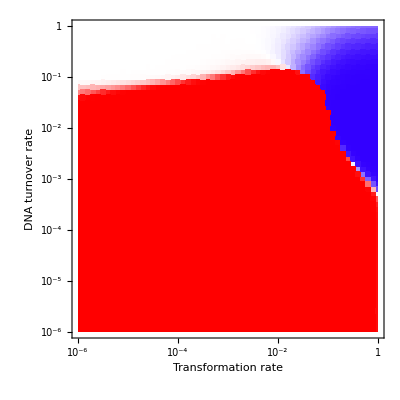

```mathematica
Table[
ListDensityPlot[ToExpression[r1],InterpolationOrder->0,FrameLabel-> {"Transformation rate","DNA turnover rate"},FrameTicks->{{{{-6,"10^-6"},{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"10^-2"},{-1,"10^-1"},{0,"1"}},None},{{{-6,"10^-6"},{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"10^-2"},{-1,"10^-1"},{0,"1"}},None}} ,BaseStyle->{FontFamily->"Arial",FontSize->20},ColorFunctionScaling->False,ColorFunction->(If[#1>0.5,Hue[0,(#1-0.5)/0.5,1],Hue[0.7,(0.5-#1)/0.5,1]]&)],{n,1,1}]
Table[
ListDensityPlot[ToExpression[r2],InterpolationOrder->0,FrameLabel-> {"Transformation rate","DNA turnover rate"},FrameTicks->{{{{-6,"10^-6"},{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"10^-2"},{-1,"10^-1"},{0,"1"}},None},{{{-6,"10^-6"},{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"10^-2"},{-1,"10^-1"},{0,"1"}},None}} ,BaseStyle->{FontFamily->"Arial",FontSize->20},ColorFunctionScaling->False,ColorFunction->(If[#1>0.5,Hue[0,(#1-0.5)/0.5,1],Hue[0.7,(0.5-#1)/0.5,1]]&)],{n,1,1}]
Table[
ListDensityPlot[ToExpression[r3],InterpolationOrder->0,FrameLabel-> {"Transformation rate","DNA turnover rate"},FrameTicks->{{{{-6,"10^-6"},{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"10^-2"},{-1,"10^-1"},{0,"1"}},None},{{{-6,"10^-6"},{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"10^-2"},{-1,"10^-1"},{0,"1"}},None}} ,BaseStyle->{FontFamily->"Arial",FontSize->20},ColorFunctionScaling->False,ColorFunction->(If[#1>0.5,Hue[0,(#1-0.5)/0.5,1],Hue[0.7,(0.5-#1)/0.5,1]]&)],{n,1,1}]
Table[
ListDensityPlot[ToExpression[r4],InterpolationOrder->0,FrameLabel-> {"Transformation rate","DNA turnover rate"},FrameTicks->{{{{-6,"10^-6"},{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"10^-2"},{-1,"10^-1"},{0,"1"}},None},{{{-6,"10^-6"},{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"10^-2"},{-1,"10^-1"},{0,"1"}},None}} ,BaseStyle->{FontFamily->"Arial",FontSize->20},ColorFunctionScaling->False,ColorFunction->(If[#1>0.5,Hue[0,(#1-0.5)/0.5,1],Hue[0.7,(0.5-#1)/0.5,1]]&)],{n,1,1}]
```

```mathematica
{}
```

```mathematica
{}
```

```mathematica
{}
```

```mathematica
{}
```

```mathematica
a1=-Graphics-;a2=-Graphics-;a3=-Graphics-;a4=-Graphics-;
```

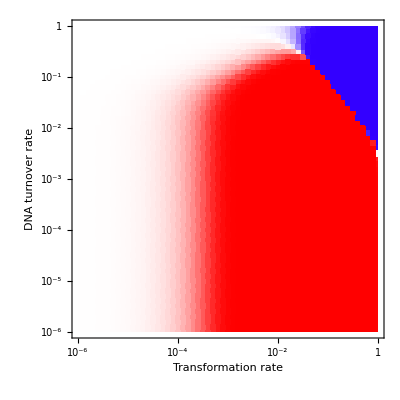
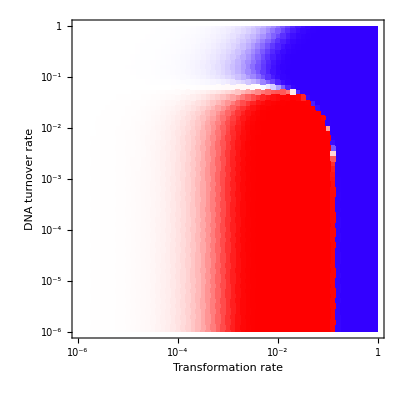
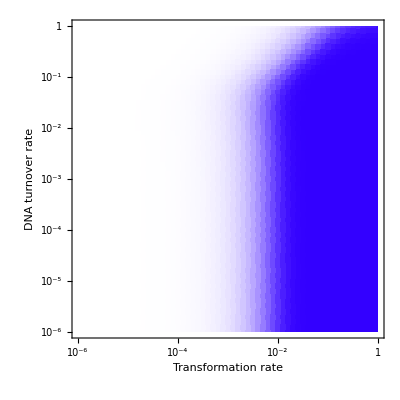
```mathematica
d1=-Graphics-;d2=-Graphics-;d3=-Graphics-;d4=-Graphics-;
```

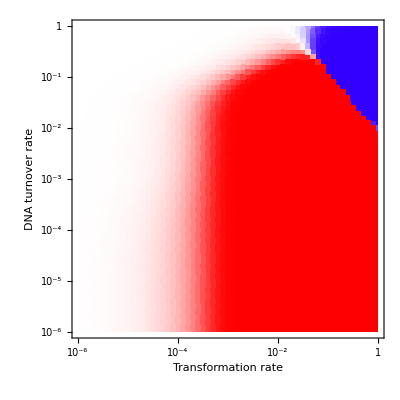
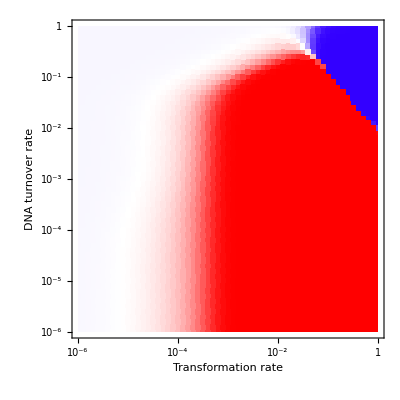
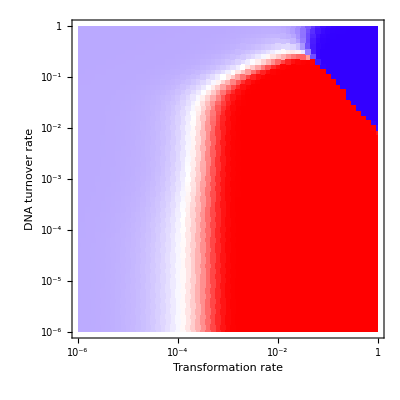
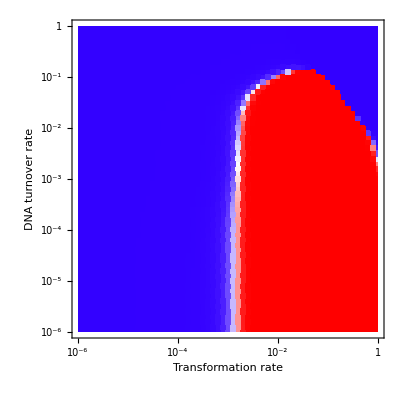
```mathematica
e1=-Graphics-;e2=-Graphics-;e3=-Graphics-;e4=-Graphics-;
```

```mathematica
Legend[max_]:=ContourPlot[y,{x,0,1},{y,0,max},FrameTicks->{{None,All},{None,None}},ColorFunctionScaling->False,ColorFunction->(If[#1>0.5,Hue[0,(#1-0.5)/0.5,1],Hue[0.7,(0.5-#1)/0.5,1]]&),Contours->200,ContourStyle->None,AspectRatio->15,Frame->{{True,True},{True,True}},FrameLabel->{Style[" ",30],None},ImageSize->{50,300},FrameStyle->20,BaseStyle->{FontFamily->"Arial",FontSize->30}];
Legend[1]
```

-Graphics-

```mathematica
GraphicsGrid[{{e1,e2},{e3,e4}},AspectRatio-> 0.87]
```

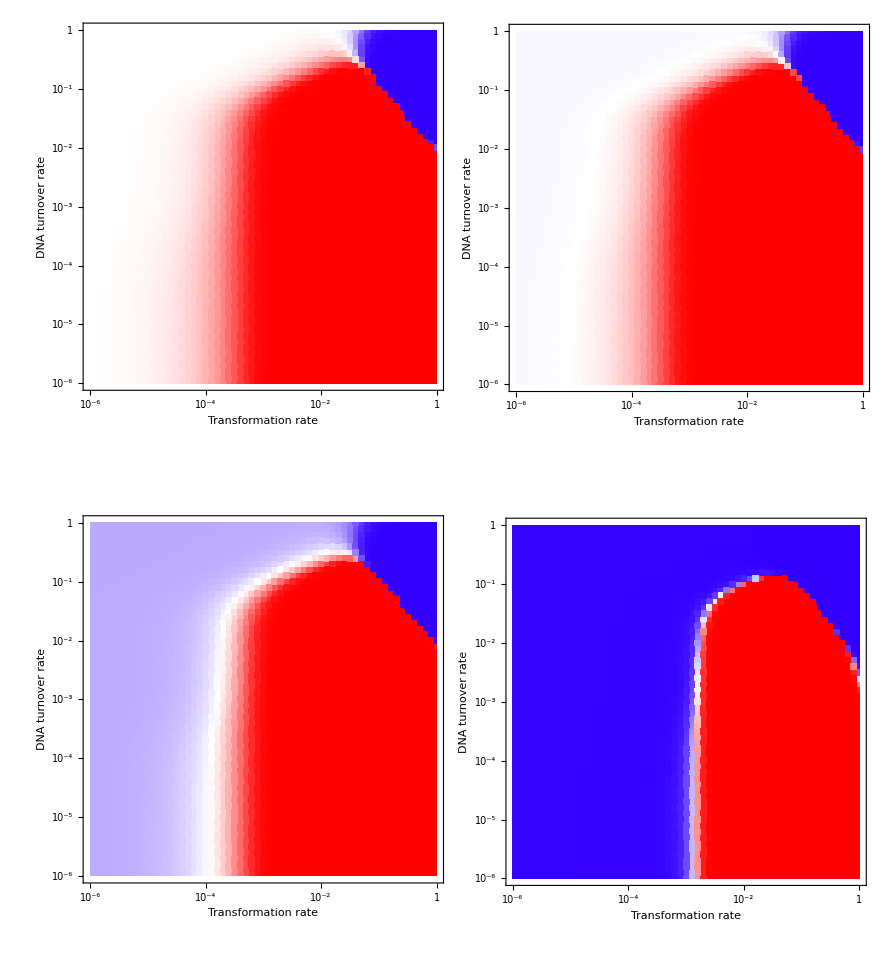

```mathematica
GraphicsGrid[{{d1,d2},{d3,d4}},AspectRatio-> 0.87]
```

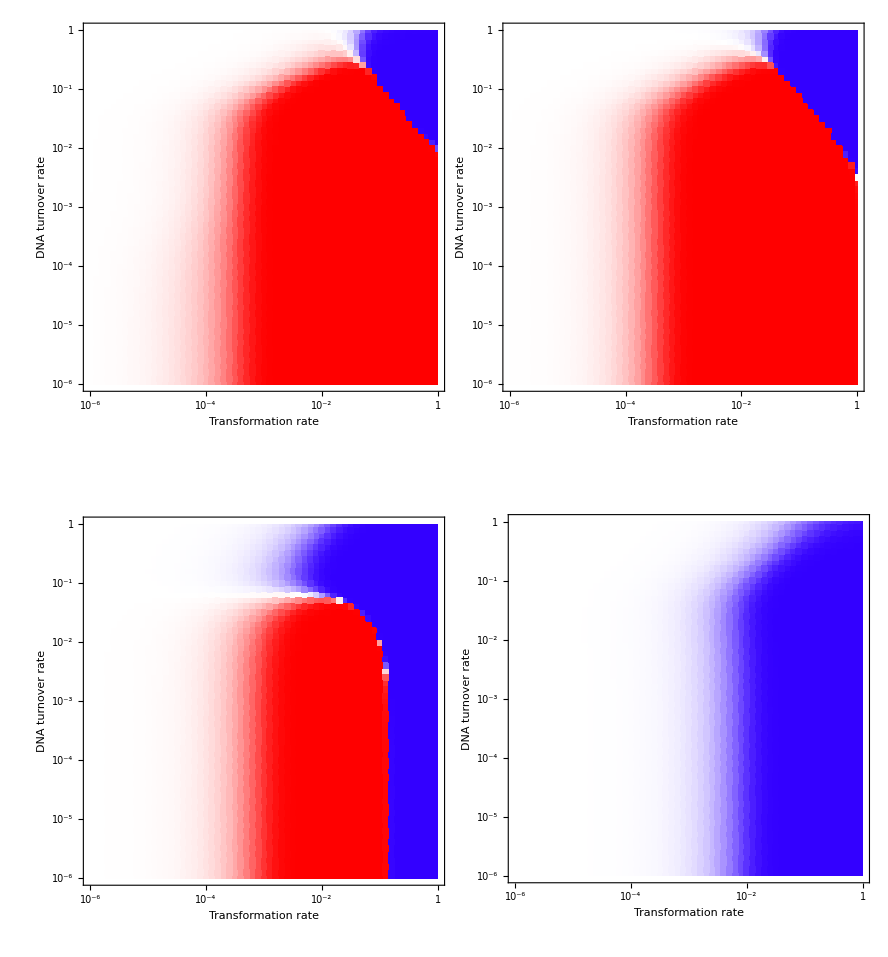

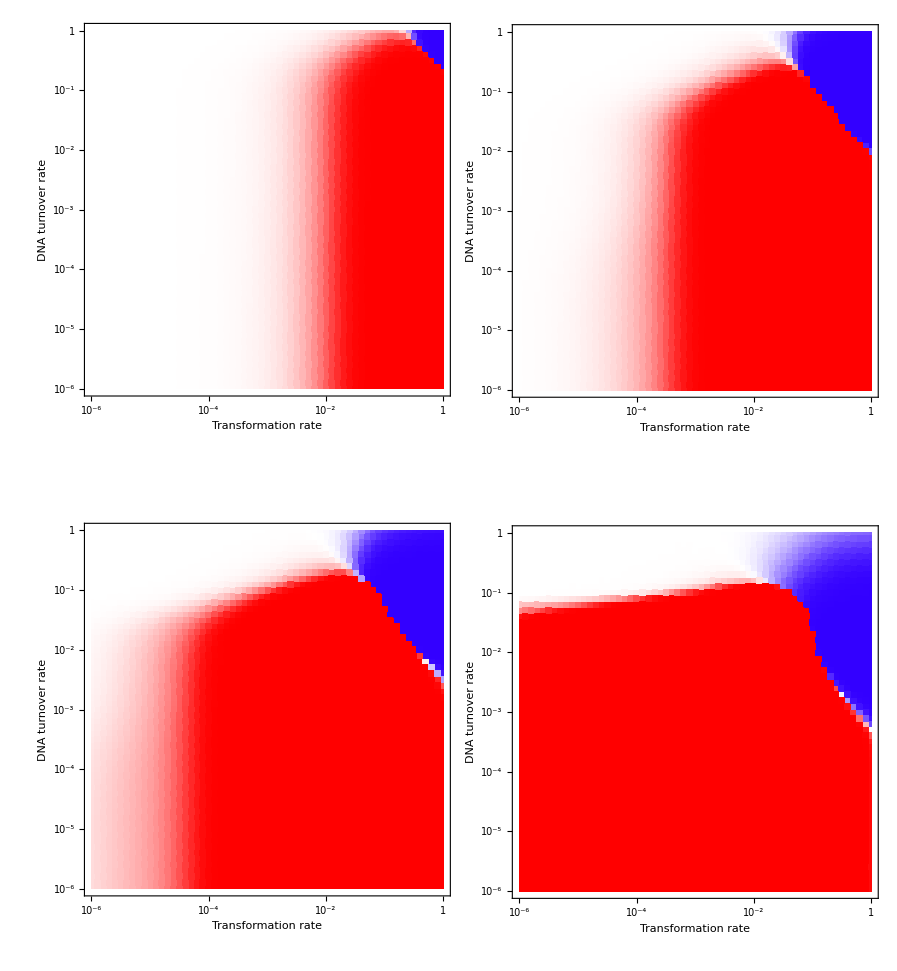

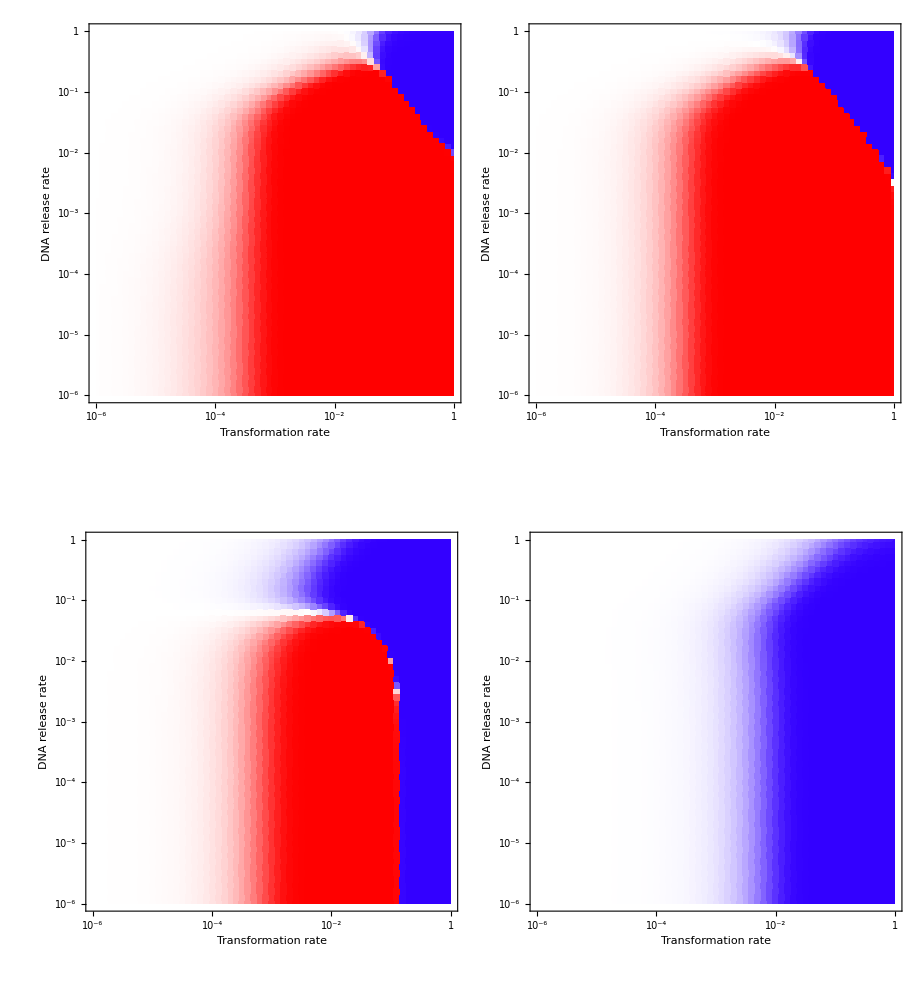

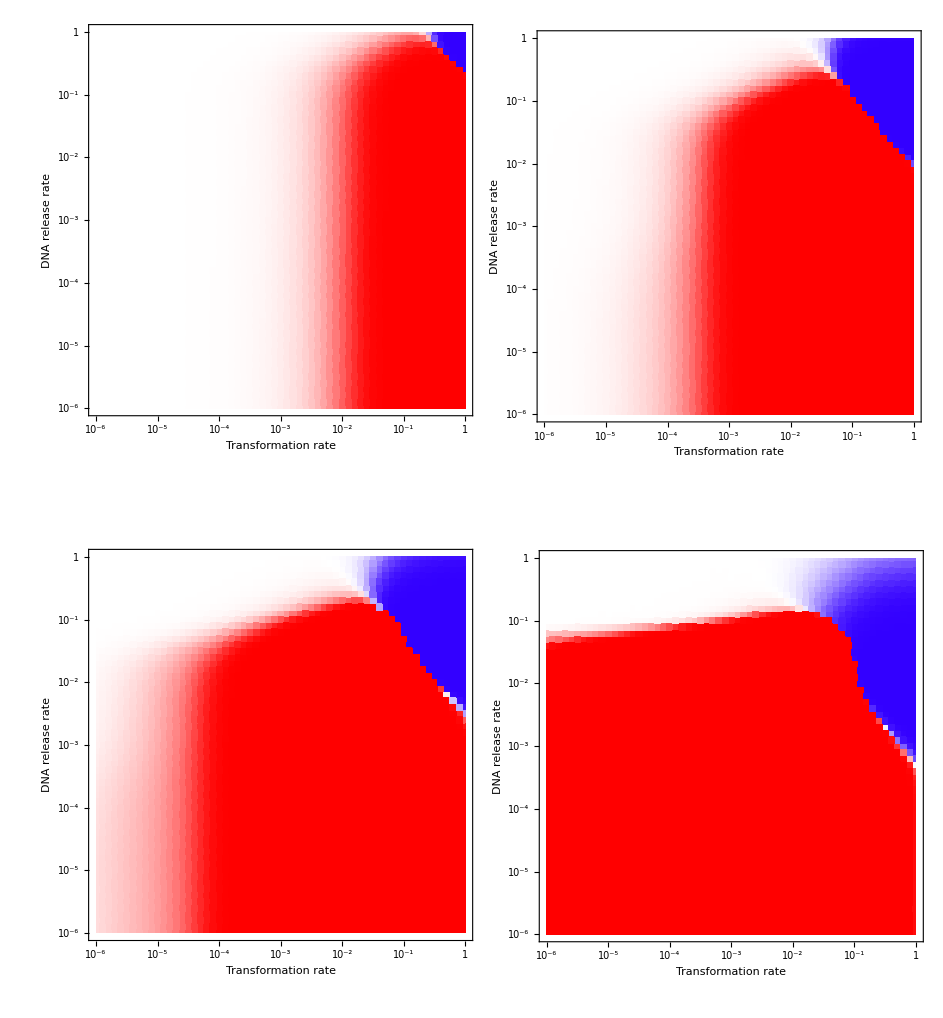

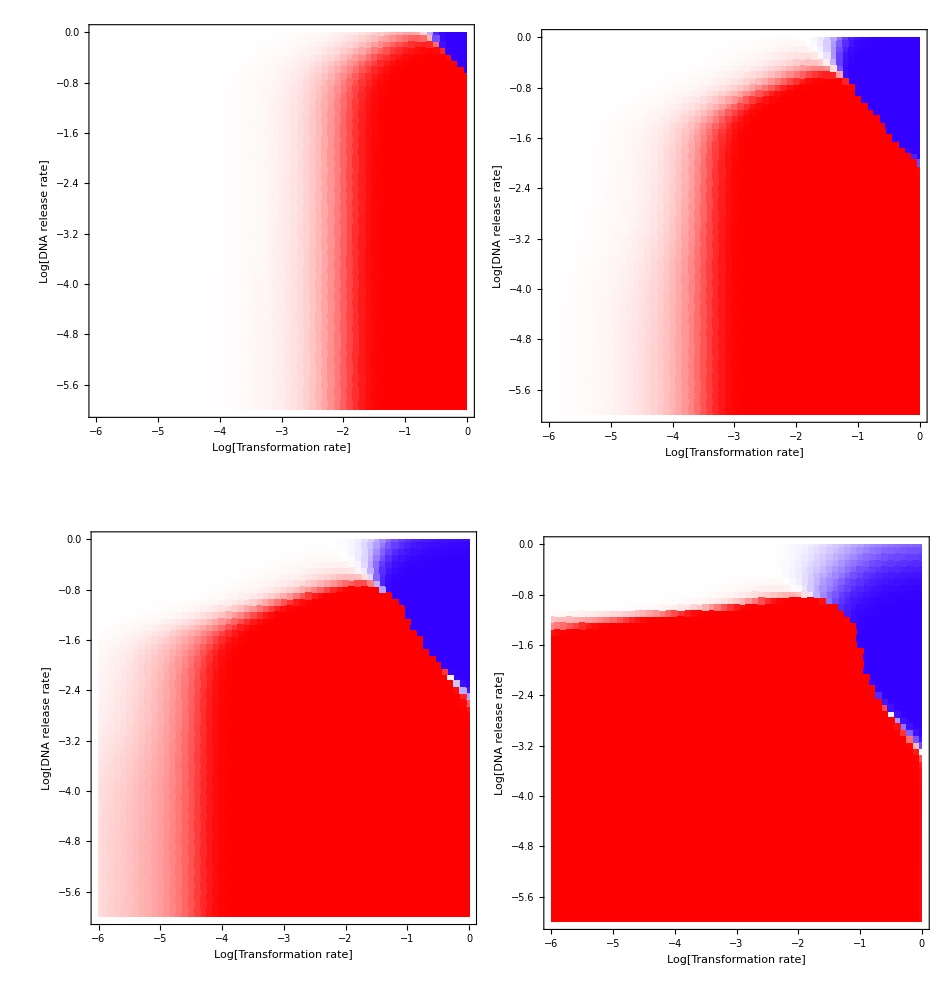

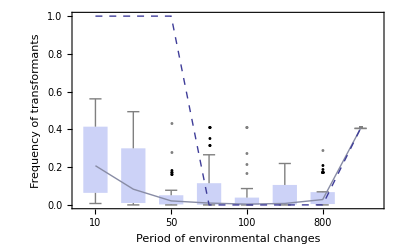
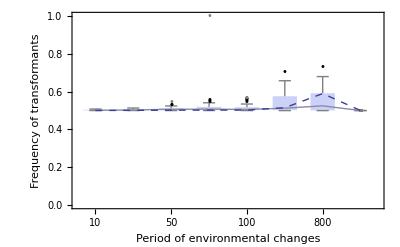
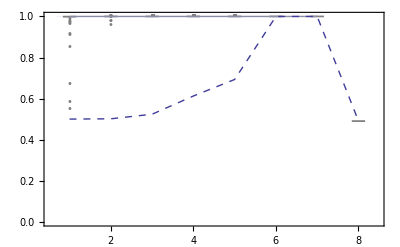
```mathematica
a1=-Graphics-;
a2=-Graphics-;
a4=-Graphics-;

a3=-Graphics-;
```

```mathematica
GraphicsGrid[{{a4,a2},{a3,a1}},AspectRatio-> 0.70]
```

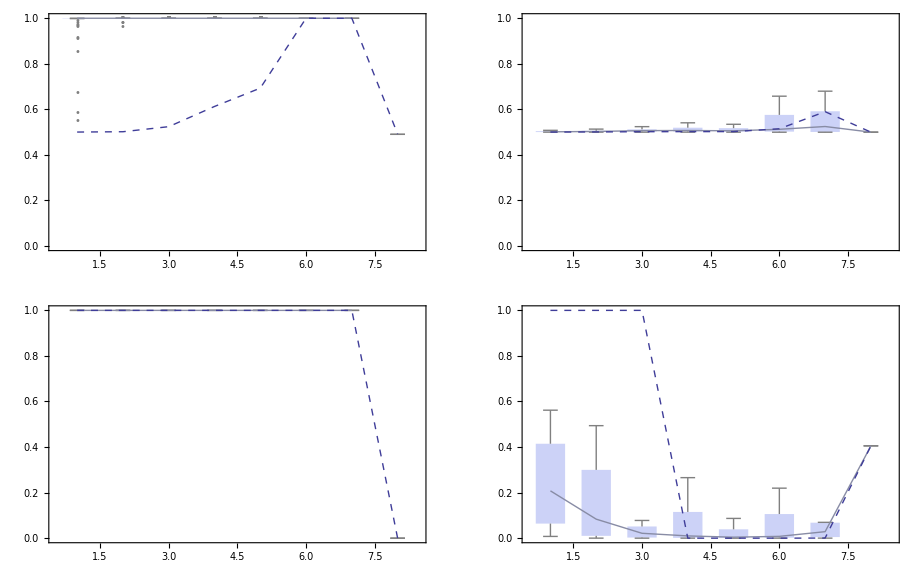

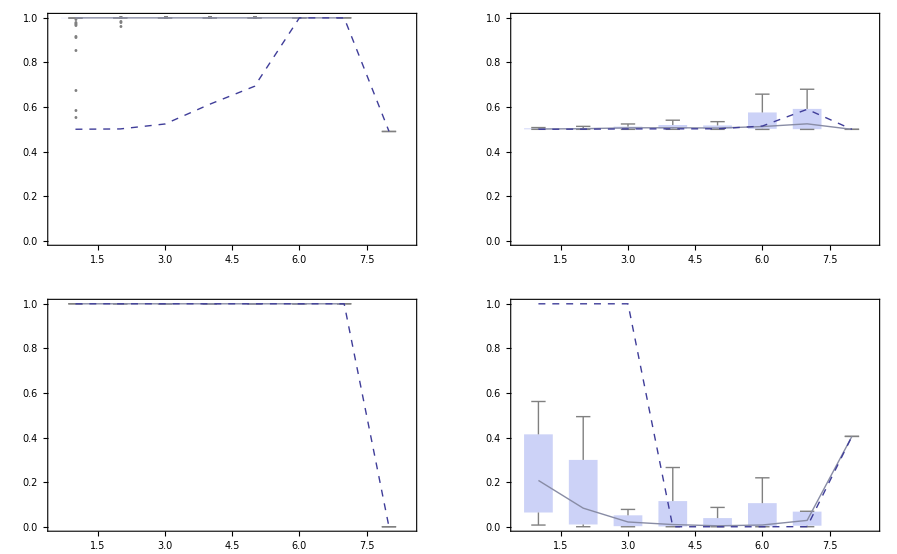

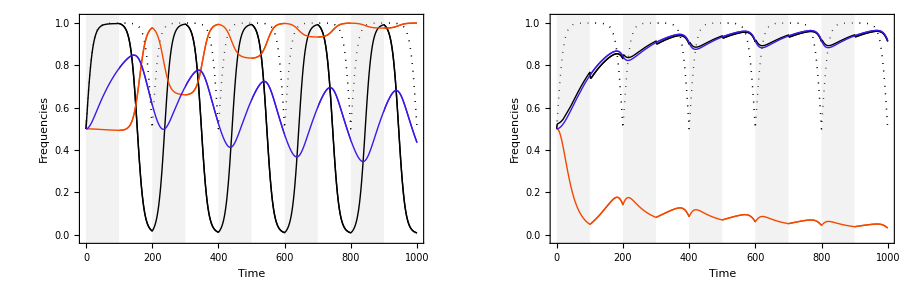

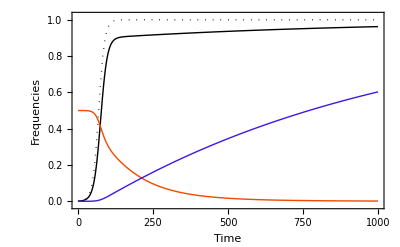

```mathematica
r2=ToExpression[r1];
rp={};
r2[[1]]

Do[
(*Print[r1[[1,n,3]]];*)
rp=Append[rp,{10^(r2[[n]][[1]]),10^(r2[[n]][[2]]),r2[[n]][[3]]}];
,{n,1,Length[r2]}]
rp
```

{-6.,-6.,0.500039}

{{1.×10^-6,1.×10^-6,0.500039},{1.25893×10^-6,1.×10^-6,0.500049},{1.58489×10^-6,1.×10^-6,0.500062},{1.99526×10^-6,1.×10^-6,0.500078},{2.51189×10^-6,1.×10^-6,0.500098},{3.16228×10^-6,1.×10^-6,0.500124},«3710»,{0.398107,1.,0.0130457},{0.501187,1.,0.00243889},{0.630957,1.,0.000579271},{0.794328,1.,0.000178896},{1.,1.,0.0000703713}}

```mathematica
Table[
ListDensityPlot[r2,InterpolationOrder->0,FrameLabel-> {"Transformation rate","DNA release rate"} ,BaseStyle->{FontFamily->"Arial",FontSize->20},ColorFunctionScaling->False,ColorFunction->(If[#1>0.5,Hue[0,(#1-0.5)/0.5,1],Hue[0.7,(0.5-#1)/0.5,1]]&)],{n,1,1}]
```

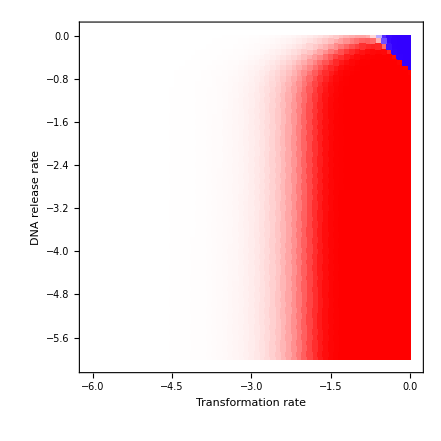

```mathematica
MatrixPlot[r2]
```

```mathematica
FrameTicks->{{{{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"10^-2"},{-1,"10^-1"},{0,"1"}},None},{{{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"10^-2"},{-1,"10^-1"},{0,"1"}},None}}
```

```mathematica
r1=Import["/Users/danesh/Documents/workspace/transformation/Res50.txt"];
r2=Import["/Users/danesh/densitymutationmm1.txt"];
r3=Import["/Users/danesh/Documents/workspace/transformation/Res50.txt"];
r4=Import["/Users/danesh/Documents/workspace/transformation/Res50.txt"];
```

```mathematica
Table[
ListDensityPlot[ToExpression[r2],InterpolationOrder->0,FrameLabel-> {"Transformation rate","DNA release rate"},FrameTicks->{{{{-6,"10^-6"},{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"10^-2"},{-1,"10^-1"},{0,"1"}},None},{{{-6,"10^-6"},{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"10^-2"},{-1,"10^-1"},{0,"1"}},None}} ,BaseStyle->{FontFamily->"Arial",FontSize->20},ColorFunctionScaling->False,ColorFunction->(If[#1>0.5,Hue[0,(#1-0.5)/0.5,1],Hue[0.7,(0.5-#1)/0.5,1]]&)],{n,1,1}]
```

{ListDensityPlot[{0.,0.,0.037132},InterpolationOrder→0,FrameLabel→{Transformation rate,DNA release rate},FrameTicks→{{{{-6,10^-6},{-5,10^-5},{-4,10^-4},{-3,10^-3},{-2,10^-2},{-1,10^-1},{0,1}},None},{{{-6,10^-6},{-5,10^-5},{-4,10^-4},{-3,10^-3},{-2,10^-2},{-1,10^-1},{0,1}},None}},BaseStyle→{FontFamily→Arial,FontSize→20},ColorFunctionScaling→False,ColorFunction→(If[#1>0.5,Hue[0,(#1-0.5)/0.5,1],Hue[0.7,(0.5-#1)/0.5,1]]&)]}

```mathematica
r2=Import["/Users/danesh/densitymutationmm3.txt"];
r3=StringSplit[r2,"}\n"];
r7={};
Do[
r5=StringDrop[r3[[m]],1];
r6=StringSplit[r5,","];
r7=Append[r7,{ToExpression[r6[[1]]],ToExpression[r6[[2]]],ToExpression[r6[[3]]]}];
,{m,1,Length[r3]}]

(*rp={};
Do[
rp=Append[rp,{r3[[n]][[1]],r3[[n]][[2]],r3[[n]][[3]]}];
,{n,1,Length[r3]}]
rp*)
```

```mathematica
Table[
ListDensityPlot[r7,InterpolationOrder->0,FrameLabel-> {"Transformation rate","DNA turnover rate"},FrameTicks->{{{{-6,"10^-6"},{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"10^-2"},{-1,"10^-1"},{0,"1"}},None},{{{-6,"10^-6"},{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"10^-2"},{-1,"10^-1"},{0,"1"}},None}} ,BaseStyle->{FontFamily->"Arial",FontSize->20},ColorFunctionScaling->False,ColorFunction->(If[#1>0.5,Hue[0,(#1-0.5)/0.5,1],Hue[0.7,(0.5-#1)/0.5,1]]&)],{n,1,1}]
```

{-Graphics-}

```mathematica
r1=-Graphics-
```

-Graphics-

```mathematica
r2=-Graphics-;
```

```mathematica
r3=-Graphics-;
```

```mathematica
r4=-Graphics-;
```

```mathematica
r2=Import["/Users/danesh/transformationRatemm2T100.txt"];
r3=StringSplit[r2,"}\n"];
r7={};
Do[
r5=StringDrop[r3[[m]],1];
r6=StringSplit[r5,","];
r7=Append[r7,{ToExpression[r6[[2]]],ToExpression[r6[[1]]],ToExpression[r6[[3]]]}];
,{m,1,Length[r3]}]
ListDensityPlot[r7,InterpolationOrder->0,FrameLabel-> {"Transformation rate^0.999","Transformation rate^0.001"},FrameTicks->{{{{-6,"10^-6"},{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"10^-2"},{-1,"10^-1"},{0,"1"}},None},{{{-6,"10^-6"},{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"10^-2"},{-1,"10^-1"},{0,"1"}},None}} ,BaseStyle->{FontFamily->"Arial",FontSize->20},ColorFunctionScaling->False,ColorFunction->(If[#1>0.5,Hue[0,(#1-0.5)/0.5,1],Hue[0.7,(0.5-#1)/0.5,1]]&)]
```

-Graphics-

```mathematica
ListDensityPlot[r7,InterpolationOrder->0,FrameLabel-> {"Transformation rate^0.999","Transformation rate^0.001"},FrameTicks->{{{{-6,"10^-6"},{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"10^-2"},{-1,"10^-1"},{0,"1"}},None},{{{-6,"10^-6"},{-5,"10^-5"},{-4,"10^-4"},{-3,"10^-3"},{-2,"10^-2"},{-1,"10^-1"},{0,"1"}},None}} ,BaseStyle->{FontFamily->"Arial",FontSize->20},ColorFunctionScaling->False,ColorFunction->(If[#1>0,Hue[0,#1,1],Hue[0.7,(-#1),1]]&)]
```

-Graphics-

```mathematica
Legend[max_]:=ContourPlot[y,{x,0,1},{y,-max,max},FrameTicks->{{None,All},{None,None}},ColorFunctionScaling->False,ColorFunction->(If[#1>0,Hue[0,(#1),3],Hue[0.7,(-#1),3]]&),Contours->300,ContourStyle->None,AspectRatio->15,Frame->{{True,True},{True,True}},FrameLabel->{Style[" ",30],None},ImageSize->{50,300},FrameStyle->20,BaseStyle->{FontFamily->"Arial",FontSize->30}];
Legend[3]
```

-Graphics-

```mathematica
q1=-Graphics-;q2=-Graphics-
```

-Graphics-

```mathematica
GraphicsGrid[{{q1,q2}},AspectRatio-> 0.870]
```